## Switching Time Analysis Pile Driver Ashwin & Aaron 1.) plot ΔT vs t_s for v_(0+) at resonance 2.) fix equations so plot 1 looks right 3. ) we’ll make other plots

```mathematica
casetimes[vop_,a_,l_,k_,m_]:= {(√(2 vop^2+4 a l)-2 vop)/(2 a),(√(vop^2+ 2 a l)- vop)/a,(√(vop^2+ 2 a l)- vop)/a+(π - ArcTan[(k(√(vop^2+2a l)))/(a √(m k))])/(√(k/m)),(√(vop^2+ 2 a l)- vop)/a+2((π - ArcTan[(k(√(vop^2+2a l)))/(a √(m k))])/(√(k/m))),2((√(vop^2+ 2 a l)- vop)/a+(π - ArcTan[(k(√(vop^2+2a l)))/(a √(m k))])/(√(k/m)))};

deltaT[ts_,vop_,a_,m_,k_,l_]:=Module[{ct},ct = casetimes[vop,a,l,k,m];
Piecewise[{{deltaTc1[ts,vop,a,l], vop^2<2 a l && ts<ct⟦1⟧}, {deltaTc2[ts,vop,a,m,k,l], ct⟦1⟧⩽ts<ct⟦2⟧}, {deltaTc3[ts,vop,a,m,k,l,ct], ct⟦2⟧⩽ts<ct⟦3⟧}, {deltaTc4[ts,vop,a,m,k,l,ct], ts==ct⟦3⟧}, {deltaTc5[ts,vop,a,m,k,l,ct], ct⟦3⟧<ts<ct⟦4⟧}, {deltaTc6[ts,vop,a,m,k,l,ct], ct⟦4⟧⩽ts<ct⟦5⟧}, {ct⟦5⟧, ct⟦5⟧≤ ts}}]
]
```

```mathematica
deltaTc1[ts_,vop_,a_,l_]:=2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2))) (* only occurs if vop^2< a l *)
deltaTc2[ts_,vop_,a_,m_,k_,l_]:=Module[{F= m a,ω= √(k/m),vts = vop+a ts,s1 = vop ts + 1/2 a ts^2,v1a,t1a,t1b,t2a,t2b},
(* what are these times?*)
v1a = √(vts^2- 2 a (l-s1));t1a = (vts-v1a)/a;t1b = ArcTan[(v1a k)/(ω F)]/ω;t2a = ArcTan[(v1a k)/(ω F)]/ω;
t2b = (√(v1a^2+ 2 a l)-v1a)/a;
ts + t1a + t1b +t2a +t2b
]
deltaTc3[ts_,vop_,a_,m_,k_,l_,ct_]:=Module[{F,ω,yt1b,t1b,vt1b,c,y0c3,t2a,v2a,t2b},F = m a;ω = √(k/m);t1b = ts - ct⟦2⟧;yt1b = (√(vop^2+ 2 a l))/ω Sin[ω t1b]-F/k Cos[ω t1b]+F/k;vt1b = √(vop^2+ 2 a l)Cos[ω t1b]+F/k ω Sin[ω t1b];
t2a = (2(ArcTan[(vt1b k + √(k (vt1b^2 k + yt1b^2 k ω^2+ 2 yt1b F ω^2)))/(ω (yt1b k + 2 F))]))/ω;
c= -1/2 m vop^2-2 F yt1b; y0c3 = (-F + √(F^2-2 k c))/k;
v2a = √(k/m y0c3^2+ 2 F/m y0c3);
t2b = (√(v2a^2+ 2 a l)- v2a)/a;
ts+t2a+ t2b
]
deltaTc4[ts_,vop_,a_,m_,k_,l_,ct_]:=Module[{F,ω,trev,y0,tfor1,v4,vimp,tfor2},F = m a;ω = √(k/m);trev=ct⟦3⟧;y0 = (F+√(F^2+k m vop^2+2F l k))/k;tfor1 = ArcCos[F/(F+k y0)]/ω;v4 = √(k/m y0^2+(2F y0)/m);vimp = √(v4^2+ 2 a l);tfor2 = (vimp-v4)/a;ts+tfor1+tfor2
]
deltaTc5[ts_,vop_,a_,m_,k_,l_,ct_]:=Module[{F,ω,t2a,y0,y2a,v2a,t2b,v2b,vimp,t2c},F = m a;ω = √(k/m); t2a = ts - ct⟦3⟧;y0 = (F+√(F^2+k m vop^2+2F l k))/k;y2a = (y0-F/k)Cos[ω t2a]+F/k;v2a = (F/k-y0)ω Sin[ω t2a]; t2b = (2 (ArcTan[(√(k (v2a^2 k+y2a^2 k ω^2+2 y2a F ω^2))+v2a k)/(ω (y2a k+2 F))]))/ω;v2b = √(2/m(1/2 k y0^2- F(2 y2a - y0)));vimp = √(v2b^2+2 a l);t2c = (vimp - v2b)/a; ts+t2b+t2c
]
deltaTc6[ts_,vop_,a_,m_,k_,l_,ct_]:=Module[{t1= ct⟦4⟧,v1,vts,sts,vimp,t2b},
v1 = √(vop^2+2 a l);vts = v1-a(ts-t1);sts = v1(ts-t1)-1/2 a(ts-t1)^2;vimp = √(vts^2+2a(l-sts));t2b = (vimp - vts)/a;ts+t2b
]
```

## Simplify math

```mathematica
FullSimplify[2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))]
```

2 ts+vop/a+√((2 a^2 ts^2+4 a ts vop+vop^2)/a^2)

```mathematica
ω = √(k/m);

FullSimplify[2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))+ω]
```

√(k/m)+2 ts+vop/a+√((2 a^2 ts^2+4 a ts vop+vop^2)/a^2)

## Make simple plot of ΔT vs t_s

{-0.104666,0.0197218,0.0249956,0.0302693,0.0499911}

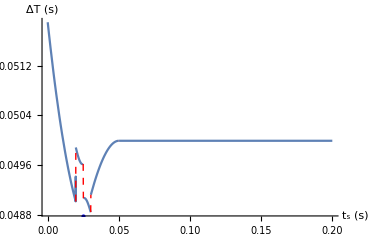

```mathematica
a=3.667;   (*please add units*)
l = 0.03;
m=0.000558;
k = 50;
vop = 0.9*1.65; (*resonant speed is ?? *)

ct = casetimes[vop,a,l,k,m]
Plot[deltaT[ts,vop,a,m,k,l],{ts,0,0.2},
Prolog->{PointSize->Large,Blue,Point[{ct⟦3⟧,deltaT[ct⟦3⟧,vop,a,m,k,l]}]},
AxesLabel->{"t_s (s)","ΔT (s)"},ExclusionsStyle->Directive[Dashed,Red],PlotRange->All
]

(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

## Make plot of ΔT vs t_s

```mathematica
casetimes[vop,a,l,k,m]
```

```mathematica
{-0.10056289600915033,0.02030780107661059,0.025299326681098147,0.030290852285585708,0.050598653362196294}
```

{-0.100563,0.0203078,0.0252993,0.0302909,0.0505987}

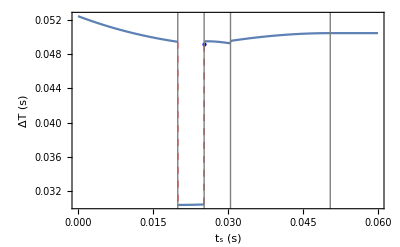

```mathematica
a=3.667;
vop = 1.63*0.9;
l = 0.03;
m=0.000558;
k = 50;
ct = casetimes[vop,a,l,k,m];

Plot[deltaT[ts,vop,a,m,k,l],{ts,0,0.06},
Frame->{True,True,False,False},FrameLabel->{"t_s (s)","ΔT (s)"},
Prolog->{PointSize->Large,Blue,Point[{ct⟦3⟧,deltaT[ct⟦3⟧,vop,a,m,k,l]}]},
Epilog->{Gray,Thin,Table[Line[{{tc,0},{tc,100}}],{ tc, ct }]},
(*Prolog-> {Gray,Opacity[0.3],Thin,Table[Rectangle[{ct⟦2tc-1⟧,0},{ct⟦2tc⟧,100}],{ tc, 1,Floor[Length[ct]/2] }]},*)
ExclusionsStyle->Directive[Dashed,Red],PlotRange->All

]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

## (simple) Make plot of ΔT vs v_(0^+)

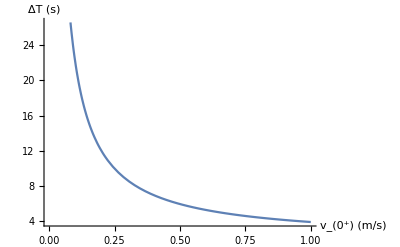

```mathematica
a=1;
ts = 1/2;
l = 0.1;
Plot[deltaTc1[ts,a,vop,l],{vop,0,1},
AxesLabel->{"v_(0^+) (m/s)","ΔT (s)"}
]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

## better plot of ΔT vs v_(0^+)

```mathematica
deltaT[0.02,1/4,a,m,k,l]
```

0.212475

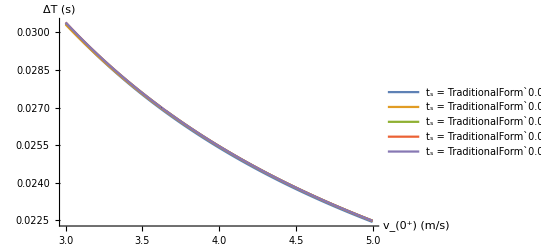

```mathematica
a=3.667;
l = 0.03;
m=0.000558;
k = 50;
tsVals = {0.01,0.022,0.027,0.040,0.06};
Clear[vop]
Plot[Evaluate[Table[deltaT[ts,vop,a,m,k,l],{ts,tsVals}]],{vop,0,5},
AxesLabel->{"v_(0^+) (m/s)","ΔT (s)"},ExclusionsStyle->Directive[Dashed,Thin],
PlotLegends->Table[StringForm["t_s = ``",ts],{ts,tsVals}]
]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```